```mathematica
h[x_]:=PDF[LogNormalDistribution[0,1],x]/(1-CDF[LogNormalDistribution[0,1],x])
```

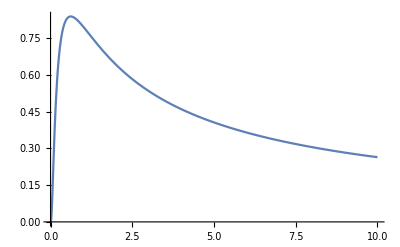

```mathematica
Plot[h[x],{x,0,10}]
```

```mathematica
h1=Animate[Plot[h[θ*x],{x,0,10},PlotRange->{0,1}],{θ,0.1,10},AnimationRunning->False,AnimationDirection->ForwardBackward, AnimationRepetitions->3]
```

```mathematica
Export["h1.gif",h1]
```

h1.gif

```mathematica
h2=Animate[Plot[θ*h[x],{x,0,10},PlotRange->{0,3}],{θ,0.1,3},AnimationRunning->False,AnimationDirection->ForwardBackward, AnimationRepetitions->3]
```

```mathematica
Export["h2.gif",h2]
```

h2.gif